# Structured Data in WL

## Wolfram Summer School 2017 Xavier Roy (xavierr@wolfram.com)

## Overview

• List

• SparseArray

• PackedArray

• Association

• Dataset

## List

• Introduction

• Extraction of elements

• Manipulation of lists

• Symbols generating lists

• Properties

## List – Introduction

• Typing lists

```mathematica
List[]
```

```mathematica
{}
```

• General construct used to represent collections of expressions

```mathematica
{1,2,3,4,5,6,7,8,9,10}
```

```mathematica
{1.8,-3.4,6.2,5.7,-9.4}
```

```mathematica
{"hello","world","!"}
```

```mathematica
{a,b,c,d,e,f,g,h,i,j}
```



```mathematica
{-Graphics-,-Graphics-,-Graphics3D-}
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
{1,"hello",-Graphics-,a,-Graphics-,g[u,v]}
```

• Lists within list

```mathematica
{1,2,3,4,5}
```

```mathematica
{{a},{b},{c},{d}}
```

```mathematica
{{a},{{{b},c},d}}
```

## List – Extraction of elements

### • Part

```mathematica
list={{a},{b},{c},{d}}
```

```mathematica
Part[list,1]
```

```mathematica
Part[list,3]
```

```mathematica
Part[list,{1,3,4}]
```

```mathematica
Part[list,{1,4,3}]
```

Counting negatively

```mathematica
list
```

```mathematica
Part[list,-1]
```

Short syntax

```mathematica
list
```

```mathematica
Part[list,1]===list[[1]]
```

Multiple levels

```mathematica
list={a,{{{b},c},d}}
```

```mathematica
Part[list,2]
```

```mathematica
Part[list,2,1]
```

```mathematica
Part[list,2,1,2]
```

### • Take - Drop

```mathematica
list={{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[1, 1, 0]},{RGBColor[1, 0.5, 0],RGBColor[0.6, 0.4, 0.2]},{RGBColor[0.5, 0, 0.5],RGBColor[1, 0.5, 0.5]},{RGBColor[0, 1, 1],RGBColor[1, 0, 1]}}
```

```mathematica
Take[list,2]
```

```mathematica
Take[list,-2]
```

```mathematica
Take[list,{2,5}]
```

```mathematica
Take[list,{1,-1,2}]
```

```mathematica
Take[list,{1,2},1]
```

### • Append - Prepend


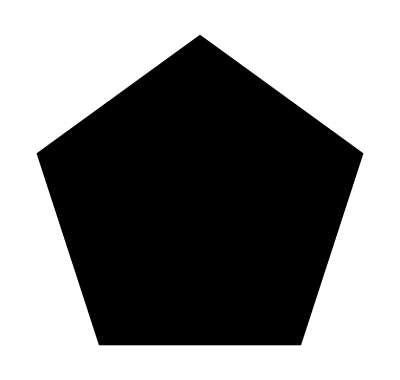
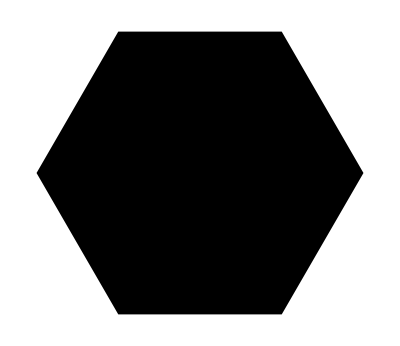
```mathematica
list={-Graphics-,-Graphics-,-Graphics-}
```

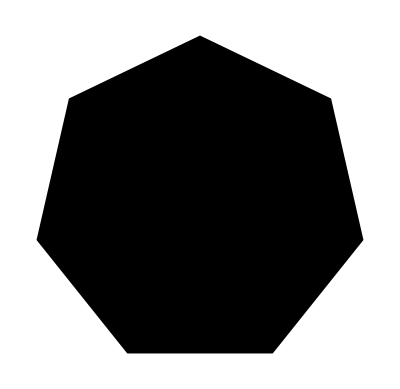
```mathematica
Append[list,-Graphics-]
```


```mathematica
Prepend[list,-Graphics-]
```

### • Insert - Delete

## List – Manipulation

### • Replace - ReplaceAll - ReplaceRepeated - ReplacePart

```mathematica
list={{a,b},{c,d,e},{a,b},{c,d,e}}
```

```mathematica
Replace[list,{a,b}->0,{1}]
```

```mathematica
Replace[list,a->0,{2}]
```

```mathematica
Replace[list,l_List/;Length[l]===3->0,{1}]
```

```mathematica
ReplacePart[list,4->0]
```

```mathematica
ReplacePart[list,{4->0,{2,3}->0}]
```

### • Map - MapAt - MapThread - MapIndexed

### • Join, Transpose, Flatten, ArrayFlatten...

## List – Symbols generating lists

### • Range

```mathematica
Range[20]
```

```mathematica
Range[10^4]
```

```mathematica
Range[1,20]
```

```mathematica
Range[6,20]
```

```mathematica
Range[6,20,2]
```

### • ConstantArray

```mathematica
ConstantArray[1,20]
```

```mathematica
ConstantArray[1,{5,5}]
```

### • Array

```mathematica
Array[f,10]
```

```mathematica
Array[f,10,5]
```

```mathematica
Array[f,{3,3}]
```

```mathematica
Array[f[#1,#2]&,{3,3}]
```

### • Table

```mathematica
Table[Mod[i,2],{i,0,10}]
```

```mathematica
Table[Mod[i,2]+Mod[j,3],{i,0,10},{j,0,10}]
```

```mathematica
Table[Mod[i,2],{i,0,10,2}]
```

## List – Symbols generating lists

• CirclePoints

```mathematica
coordinates=CirclePoints[5]
```

```mathematica
Graphics[Polygon[coordinates]]
```

• SpherePoints

```mathematica
(coordinates=SpherePoints[200])//Short
```

```mathematica
Graphics3D[Point[coordinates]]
```

• ColorSeparate

```mathematica
ColorSeparate[-Graphics-]
```

```mathematica
ColorSeparate[-Graphics-,"CMYK"]
```

• AnglePath

```mathematica
AnglePath[{90°,90°,90°}]
```

```mathematica
transformations=AnglePath[{0,0},{{4,45°},{3 √2,-45°}},"RotationTranslation"]
```

```mathematica
turtle=-Graphics-;
Graphics[GeometricTransformation[turtle[[1]],transformations]]
```

• Alphabet

```mathematica
Alphabet[]
```

```mathematica
Alphabet["Greek"]
```

```mathematica
Alphabet[Entity["Language","Russian"]]
```

## List – Properties

• Length, Depth and Dimensions

```mathematica
list=CharacterRange["A","z"]
```

```mathematica
Length[list]
```

```mathematica
Depth[list]
```

```mathematica
Dimensions[list]
```

```mathematica
array=Table[10i+j,{i,4},{j,3}]
```

```mathematica
Length[array]
```

```mathematica
Dimensions[array]
```

• Structural tests

```mathematica
vec=Range[10]
VectorQ[vec]
```

```mathematica
mat=SpherePoints[10^4]
MatrixQ[mat]
```

```mathematica
arr=Array[f,{3,3,3}]
ArrayQ[arr]
```

```mathematica
VectorQ[list]
```

## SparseArray

• Introduction

• Why using them?

• Manipulation of sparse arrays

• Properties

## SparseArray - Introduction

### What are they?

• Used to efficiently represent and compute with lists (or nested lists) that have a constant (often 0) “background” value. A SparseArray can be expanded to a full-dimensional List using Normal.

### Constructions of sparse arrays

• Using rules to specify values at positions

```mathematica
SparseArray[1->5,10]
Normal[%]
```

```mathematica
SparseArray[{1->5,2->5},10]
Normal[%]
```

```mathematica
SparseArray[{1->5,2->5},10,2]
Normal[%]
```

```mathematica
SparseArray[{{1,2}->2,{4,3}->2},{5,5},-10]
Normal[%]
```

• Using rules with patterns

```mathematica
SparseArray[{
i_/;Mod[i,15]===0->"fizzbuzz",
i_/;Mod[i,3]===0->"fizz",
i_/;Mod[i,5]===0->"buzz"
},100]
```

```mathematica
SparseArray[{i_,i_}->1,{5,5}]
MatrixForm@Normal[%]
```

• Converting a list to a sparse array

```mathematica
list={0,0,0,4,2,0,8}
```

```mathematica
SparseArray[list]
```

```mathematica
list={1,1,1,4,2,1,8}
```

```mathematica
SparseArray[list]
```

```mathematica
SparseArray[list,Dimensions[list],1]
```

```mathematica
SparseArray[list,Automatic,1]
```

• SparseArray need to be arrays

```mathematica
list={1,{2}}
```

```mathematica
ArrayQ[list]
```

```mathematica
SparseArray[list]
```

```mathematica
SparseArray[{1->1,2->{2}}]
```

## SparseArray - Introduction

• Constructing sparse arrays with Band

```mathematica
DiagonalMatrix[ConstantArray[x,5]];
MatrixForm[%]
```

```mathematica
sarr=SparseArray[Band[{1,1}]->x,{5,5}];
MatrixForm[sarr]
```

```mathematica
sarr=SparseArray[{Band[{1,1}]->x,Band[{2,1}]->y},{5,5}];
MatrixForm[sarr]
```

```mathematica
sarr=SparseArray[{Band[{1,1},{3,3}]->x,Band[{2,1},{4,3}]->y},{5,5}];
MatrixForm[sarr]
```

```mathematica
sarr=SparseArray[{Band[{1,1},{3,3},2]->x,Band[{2,1},{4,3},2]->y},{5,5}];
MatrixForm[sarr]
```

## SparseArray - Why and when using them?

### Compact representation

```mathematica
m=SparseArray[{i_,i_}:>10,{100,100}]
```

```mathematica
diagmat=DiagonalMatrix[ConstantArray[10,100]];
m==diagmat
```

```mathematica
ByteCount[m]
```

```mathematica
ByteCount[diagmat]
```

### Efficient computation

```mathematica
sp=SparseArray[{i_,i_,i_}:>10,{10^3,10^3,10^2}];
nsp=Normal[sp,SparseArray];
```

```mathematica
Part[sp,1;;10];//AbsoluteTiming
```

```mathematica
Part[nsp,1;;10];//AbsoluteTiming
```

```mathematica
Transpose[sp];//AbsoluteTiming
```

```mathematica
Transpose[nsp];//AbsoluteTiming
```

### Represent data too large to be represented in normal form:

```mathematica
s=SparseArray[{{i_,i_}->i},{100000,100000}]
```

```mathematica
s["Density"]
```

```mathematica
Normal[s]
```

## SparseArray - Manipulation

### • ArrayRules

```mathematica
sarr=SparseArray[{Band[{1,1},Automatic,2]->1,Band[{2,1},Automatic,2]->2},{5,5}]
MatrixForm[sarr]
```

```mathematica
ArrayRules[sarr]
```

### • Symbols manipulating lists works with SparseArray

```mathematica
sarr=SparseArray[{i_,i_,i_}->1,{100,100,100}]
```

```mathematica
Part[sarr,1]
```

```mathematica
Part[sarr,1,{50,75}]
```

```mathematica
Take[sarr,50,25,10]
```

### • Append - Prepend

```mathematica
sarr=SparseArray[{i_,i_}:>i,{50}]
```

```mathematica
Append[sarr,1]
Normal[%]
```

```mathematica
sarr=SparseArray[{i_,i_}:>i,{10,2}]
```

```mathematica
Append[sarr,{1,1}]
Normal[%]
```

```mathematica
sarr=SparseArray[{i_,i_}:>i,{10,2}]
```

```mathematica
Append[sarr,1]
```

```mathematica
ArrayQ[%]
```

### • Insert - Delete

### • Replace - ReplaceAll - ReplaceRepeated - ReplacePart

### • Map - MapAt - MapThread - MapIndexed

### • Join, Transpose, Flatten, ArrayFlatten...

## SparseArray - Properties

```mathematica
sarr=SparseArray[{i_,i_}:>i,{50,50}]
```

```mathematica
sarr["Properties"]
```

```mathematica
sarr["Background"]
```

```mathematica
sarr["NonzeroValues"]
```

```mathematica
sarr["Density"]
```

```mathematica
sarr["PatternArray"]
MatrixForm[%]
```

## StructuredArray

### What are they?

• Two types of structured arrays
– SymmetrizedArray
– QuantityArray

### SymmetrizedArray

• Construction

```mathematica
sa=SymmetrizedArray[{{1,2}->a,{1,2}->b,{2,1}->c},{2,2},Symmetric[{1,2}]]
```

```mathematica
Normal[sa,StructuredArray]
```

```mathematica
sa=SymmetrizedArray[{{{a,b},{b,c}},{{b,c},{c,d}}}]
```

```mathematica
SymmetricMatrixQ[sa]
```

• Compact and memory-efficient representation of arrays with symmetries

```mathematica
CrossMatrix[{2,2,2}]
```

```mathematica
SymmetrizedArray[%]
```

```mathematica
ByteCount[cross=CrossMatrix[{10, 10, 10, 10}]]
```

```mathematica
ByteCount[SymmetrizedArray[cross]]
```

### QuantityArray

• Construction

```mathematica
QuantityArray[{1},"Meters"]
```

```mathematica
QuantityArray[{1,2},{"Meters","Seconds"}]
```

```mathematica
QuantityArray[{{1,2},{1,2}},{"Meters","Seconds"}]
```

• Memory-efficient representation of arrays of quantities.

```mathematica
qa=GeoElevationData[GeoDisk[Entity["Mountain","MountEverest"],Quantity[3, "Miles"]]]
```

```mathematica
qa[[100,1;;20]]
%//Normal
```

```mathematica
nqa=Normal[qa,StructuredArray];
ByteCount[qa]/ByteCount[nqa]//N
```

• Faster extraction of magnitudes and units:

```mathematica
QuantityMagnitude[qa];//AbsoluteTiming
```

```mathematica
QuantityMagnitude[nqa]; // AbsoluteTiming
```

## PackedArray

• Introduction

• Why and when to use them?

• Packing expressions

## PackedArray - Introduction

### What are they?

Lists, vectors, matrices... in general arrays, that have a compact and memory efficient internal representation.

```mathematica
?Developer`*Packed*
```

RowBox[{"PackedArrayForm", "[", StyleBox["expr", "TI"], "]"}] prints with packed arrays in StyleBox["expr", "TI"] shown in summary form, without all their elements explicitly given.

### PackedArrayQ

```mathematica
list=Range[100];
Developer`PackedArrayQ[list]
```

True

```mathematica
list=ConstantArray[1,10^4];
Developer`PackedArrayQ[list]
```

True

```mathematica
list=Table[1,10^4];
Developer`PackedArrayQ[list]
```

True

```mathematica
list={1,2,3,4,5,6,7,8,9};
Developer`PackedArrayQ[list]
```

False

### ToPackedArray & FromPackedArray

```mathematica
list={1,2,3,4,5,6,7,8,9}
Developer`PackedArrayQ[list]
```

{1,2,3,4,5,6,7,8,9}

False

```mathematica
packedlist=Developer`ToPackedArray[list]
Developer`PackedArrayQ[packedlist]
```

{1,2,3,4,5,6,7,8,9}

True

```mathematica
Developer`PackedArrayForm[packedlist]
```

PackedArray[Integer,<9>]

```mathematica
unpackedlist=Developer`FromPackedArray[packedlist]
Developer`PackedArrayQ[unpackedlist]
```

{1,2,3,4,5,6,7,8,9}

False

## PackedArray - Why and when to use them?

```mathematica
list=ConstantArray[10,{10^3,10^3}];
Developer`PackedArrayQ[list]
```

True

```mathematica
ulist=Developer`FromPackedArray[list];
Developer`PackedArrayQ[ulist]
```

False

Memory efficient

```mathematica
ByteCount[list]
ByteCount[ulist]
```

8000152

24208200

Time efficient for operations

```mathematica
list*list;//AbsoluteTiming
```

```mathematica
ulist*ulist;//AbsoluteTiming
```

```mathematica
Transpose[list];//AbsoluteTiming
```

{0.00798088,Null}

```mathematica
Transpose[ulist];//AbsoluteTiming
```

{0.073462,Null}

## PackedArray - Packing expressions

### Integers

```mathematica
list={1,2,3,4,5};
plist=Developer`ToPackedArray[list]
```

{1,2,3,4,5}

```mathematica
Developer`PackedArrayQ[plist]
```

True

### Reals

```mathematica
list={1.5,-2.8,3.6,4.8,5.4};
plist=Developer`ToPackedArray[list]
```

{1.5,-2.8,3.6,4.8,5.4}

```mathematica
Developer`PackedArrayQ[plist]
```

True

### Can we pack anything?

```mathematica
list={1,2,3,4,5.7};
plist=Developer`ToPackedArray[list]
```

{1,2,3,4,5.7}

```mathematica
Developer`PackedArrayQ[plist]
```

False

```mathematica
list={1,2,3,4,5};
plist=Developer`ToPackedArray[list];
Append[plist,6]
Developer`PackedArrayQ[%]
```

{1,2,3,4,5,6}

True

```mathematica
list={1,2,3,4,5};
plist=Developer`ToPackedArray[list];
Append[plist,6.5]
Developer`PackedArrayQ[%]
```

{1,2,3,4,5,6.5}

False

### Additional properties

```mathematica
list=ConstantArray[10,10^6];
Developer`PackedArrayQ[list]
```

True

```mathematica
VectorQ[list,NumericQ]//AbsoluteTiming
```

{6.84247×10^-6,True}

```mathematica
ulist=Developer`FromPackedArray[list];
Developer`PackedArrayQ[ulist]
```

False

```mathematica
VectorQ[ulist,NumericQ]//AbsoluteTiming
```

{0.00568438,True}

## Association

• Introduction

• Extraction of elements

• Manipulation of associations

• Symbols generating associations

• Why and when using them?

## Association - Introduction

### What are they?

Generalization of:
– symbolically indexed lists, 
– associative arrays, 
– dictionaries, 
– hashmaps, 
– ...

An Association is so named because it associates keys with values, allowing highly efficient lookup and updating even with millions of elements.

• Typing associations

```mathematica
Association[]
```

```mathematica
<||>
```

• Associations can contained anything

```mathematica
Association[a->1,b->2,c->3]
```

```mathematica
Association[a->1.5,b->2.9,c->-3.7]
```

```mathematica
Association[a->-Graphics-,b->"hello",c->-Graphics-]
```

```mathematica
Association["a"->-Graphics-,3->"hello",f[a,b]->-Graphics-]
```

```mathematica
Association[a->(Print[1];1),b->2,c->3]
```

```mathematica
Association[a:>(Print[1];1),b->2,c->3]
```

• Associations can contain associations

```mathematica
Association[a->Association[x->1,y->2,z->3],b->2,c->3]
```

<|a→<|x→1,y→2,z→3|>,b→2,c→3|>

```mathematica
Association[a->Association[x->1,y->Association[α->1,β->2,γ->3],z->3],b->2,c->3]
```

<|a→<|x→1,y→<|α→1,β→2,γ→3|>,z→3|>,b→2,c→3|>

• If keys are identical, the last one wins:

```mathematica
Association[a->1,b->2,a->3]
```

<|a→3,b→2|>

## Association - Extraction of elements

### Key-Value pairs

```mathematica
assoc=<|"a"->u,"b"->v,"c"->w,"d"->x,"e"->y,"f"->z|>
```

<|a→u,b→v,c→w,d→x,e→y,f→z|>

```mathematica
Part[assoc,{2,-1}]
```

<|b→v,f→z|>

```mathematica
Take[assoc,{2,5}]
```

<|b→v,c→w,d→x,e→y|>

### Keys

```mathematica
assoc=<|"a"->u,"b"->v,"c"->w,"d"->x,"e"->y,"f"->z|>
```

<|a→u,b→v,c→w,d→x,e→y,f→z|>

```mathematica
Keys[assoc]
```

{a,b,c,d,e,f}

### Values

```mathematica
assoc=<|"a"->u,"b"->v,"c"->w,"d"->x,"e"->y,"f"->z|>
```

```mathematica
Values[assoc]
```

{u,v,w,x,y,z}

```mathematica
assoc["b"]
```

v

```mathematica
assoc["f"]
```

z

```mathematica
Lookup[assoc,"b"]
```

v

```mathematica
Lookup[assoc,"aa"]
```

Missing[KeyAbsent,aa]

```mathematica
Lookup[assoc,"aa",p]
```

p

## Association - Manipulation

### With respect to the keys

```mathematica
assoc=<|"a"->u,"b"->v,"c"->w,"d"->x,"e"->y,"f"->z|>
```

<|a→u,b→v,c→w,d→x,e→y,f→z|>

```mathematica
KeyTake
KeySort
KeySelect
KeyExistsQ
```

### With respect to the values

Any of the symbols for list manipulation works

```mathematica
Join
Transpose
Map
Append
Prepend
Sort
```

## Association - Symbols generating associations

• Constructing associations

```mathematica
AssociationThread[Range[26]->RandomSample@CharacterRange["a","z"]]
```

```mathematica
AssociationMap[f,{a,b,c,d}]
```

• GroupBy

```mathematica
GroupBy[{{a,b},{a,c},{b,c}},First]
```

```mathematica
GroupBy[{{a,b},{a,c},{b,c}},First->Last]
```

```mathematica
GroupBy[<|a->1,b->2,c->3|>,EvenQ]
```

```mathematica
GroupBy[<|a->1,b->2,c->4|>,{EvenQ,PrimeQ}]
```

• Counts - CountsBy

```mathematica
Counts[RandomInteger[{0,1},100]]
```

```mathematica
CountsBy[Range[1000],PrimeQ]
```

## Association - Why and when using them?

### Memory and performance comparison

• Storage

```mathematica
list=Range[10^6];
ByteCount[list]
```

```mathematica
assoc=AssociationThread[list,list];
ByteCount[assoc]
```

• Extraction

```mathematica
list[[10^5]];//AbsoluteTiming
```

```mathematica
assoc[[10^5]];//AbsoluteTiming
```

```mathematica
Lookup[assoc,10^5];//AbsoluteTiming
```

```mathematica
assoc[[10^5]]===Lookup[assoc,10^5]
```

• Insertion

```mathematica
Insert[list,10^6+1,-1];//MaxMemoryUsed
```

```mathematica
Insert[assoc,10^6+1->10^6+1,-1];//MaxMemoryUsed
```

```mathematica
Insert[list,10^6+1,-1];//AbsoluteTiming
```

```mathematica
Insert[assoc,10^6+1->10^6+1,-1];//AbsoluteTiming
```

• Deletion

```mathematica
Delete[list,-1];//MaxMemoryUsed
```

```mathematica
Delete[assoc,-1];//MaxMemoryUsed
```

```mathematica
Delete[list,-1];//AbsoluteTiming
```

```mathematica
Delete[assoc,-1];//AbsoluteTiming
```

## Dataset

### What are they?

Structured data set based on a hierarchy of lists and associations

### Construction

|  | {{◻,◻,◻},
{◻,◻,◻},
{◻,◻,◻},
{◻,◻,◻}}
     list of lists | 
a table without named rows and columns
       |  | 
{<|"x"→◻,"y"→◻,…|>,
<|"x"→◻,"y"→◻,…|>,
<|"x"→◻,"y"→◻,…|> }
             list of associations | 

a table with named columns 
       |  | <|"a"→{◻,◻},
  "b"→{◻,◻},
  "c"→{◻,◻},
  "d"→{◻,◻}|> 
     association of lists | 

a table with named rows
       |  | <|"a"→<|"x"→◻,"y"→◻|>,
  "b"→<|"x"→◻,"y"→◻|>,
  "c"→<|"x"→◻,"y"→◻|>|> 
             association of  associations | 
a table with named columns and named rows

```mathematica
lists={{1,2,3},{10,11,12},{20,21,22}}
Dataset[lists]
```

```mathematica
assocs=AssociationThread[{"x","y","z"}->#]&/@{{1,2,3},{10,11,12},{20,21,22}};
Dataset[assocs]
```

```mathematica
data=AssociationThread[{"a","b","c"}->assocs];
Dataset[data]
```